```mathematica
51-25
77-51
```

26

26

```mathematica
size=101;
num=5;
pts=({{51, 26}, {51, 76}, {51, 51}, {76, 51}, {26, 51}})(*RandomInteger[{1,size},{num,2}]*);

map=Table[
idx=1;
dist=EuclideanDistance[{i,j},pts⟦1⟧];

Do[
d2=EuclideanDistance[{i,j},pts⟦k⟧];
If[d2<dist,dist=d2;idx=k;];
,{k,2,num}];
idx/(num+1)
,{i,size},{j,size}];

Do[map⟦pts⟦k,1⟧,pts⟦k,2⟧⟧=0,{k,num}]
```

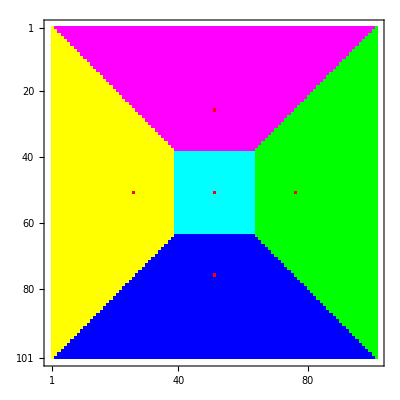

```mathematica
MatrixPlot[map,ColorFunction->Hue,ColorFunctionScaling->False]
```

```mathematica
map//Flatten//Tally
```

{{1/6,2275},{1/3,2249},{0,5},{1/2,1249},{2/3,2224},{5/6,2199}}